# Rectangle

### Author

Eric W. Weisstein
August 27, 2010

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Polygons/Rectangle.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/Rectangle.html.

©2010 Wolfram Research, Inc. except for portions noted otherwise

## Figure

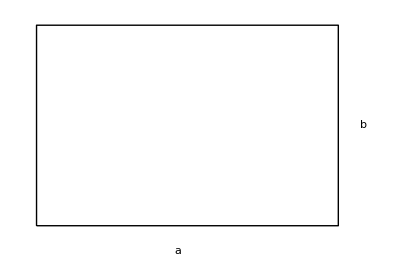

```mathematica
Block[{a=.6,b=.4},Graphics[{
Line[{{0,0},{a,0},{a,b},{0,b},{0,0}}],
Text[Style["a",Italic],{a/2-.02,-.05}],
Text[Style["b",Italic],{a+.05,b/2+.00}]
}]]
```

## Properties

Rehashing named triangle objects...

### Cricumradius

```mathematica
Manipulate[Graphics[{Line[{{-a,-b},{a,-b},{a,b},{-a,b},{-a,-b}}/2],Blue,Circle[{0,0},Sqrt[a^2+b^2]/2]}],{{a,1},1,5},{{b,1},1,5}]
```

### Inequality

```mathematica
ineq[x_,y_]:=-a/2≤x≤a/2&&-b/2≤y≤b/2
```

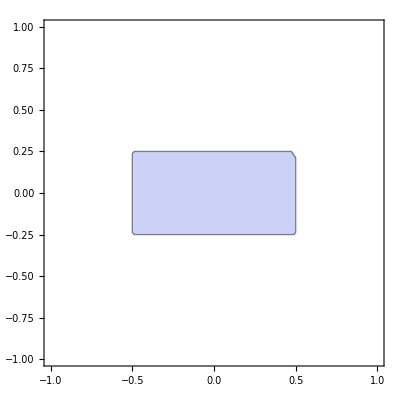

```mathematica
RegionPlot[ineq[x,y]/.{a->1,b->1/2},{x,-1,1},{y,-1,1}]
```

### Centroid

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionaliy. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

System`EdgeColor::shdw: Symbol "EdgeColor" appears in multiple contexts {"System`", "Combinatorica`"}; definitions in context "System`" may shadow or be shadowed by other definitions.

```mathematica
Assuming[a>0,Centroid[ineq[x,y],{x,y}]]//FullSimplify//Timing
```

{0.474506,{0,0}}

```mathematica
Assuming[a>0&&b>0,Simplify@RegionCentroid[Rectangle[-{a,b}/2,{a,b}/2]]]
```

{0,0}

### Area

```mathematica
Assuming[a>0&&b>0,Area[ineq[x,y],{x,y}]]//FullSimplify//Timing
```

{0.129678,a b}

```mathematica
Assuming[a>0&&b>0,Integrate[1,{x,y}∈Rectangle[-{a,b}/2,{a,b}/2]]]
```

ConditionalExpression[a b,a>0&&b>0]

```mathematica
Assuming[a>0&&b>0,Simplify@Integrate[1,{x,y}∈Rectangle[-{a,b}/2,{a,b}/2]]]
```

a b

```mathematica
Assuming[a>0&&b>0,RegionMeasure[Rectangle[-{a,b}/2,{a,b}/2]]]
```

a b

### InertiaTensor

```mathematica
FullSimplify[Assuming[a>0,AreaInertiaTensor[ineq[x,y],{x,y}]],a>0&&b>0]
```

{{(a b^3)/12,0},{0,(a^3 b)/12}}

### RadiiOfGyration

```mathematica
Assuming[a>0&&b>0,FullSimplify[RadiiOfGyration[ineq[x,y],{x,y}]]]
```

{b/(2 √3),a/(2 √3)}

### GeneralizeDiameter

```mathematica
ineqs=FullSimplify[And@@ineq@@@{{x1,y1},{x2,y2}},a>0]
```

a+2 x1≥0&&a≥2 x1&&b+2 y1≥0&&b≥2 y1&&a+2 x2≥0&&a≥2 x2&&b+2 y2≥0&&b≥2 y2

```mathematica
FullSimplify[Maximize[{(x1-x2)^2+(y1-y2)^2,ineqs&&a>0&&b>0},{x1,x2,y1,y2},Reals],a>0&&b>0]//Timing
```

{4.40048,{a^2+b^2,{x1→-a/2,x2→a/2,y1→-b/2,y2→b/2}}}